# Graphs

In this lab, we will investigate graphs and their properties by using the House of Graphs: https://houseofgraphs.org/

## Finding interesting graphs

Suppose that we want to find a graph that has diameter 3 (meaning that any two vertices are connected by a path of at most 3) and chromatic number 5. We also require that the graph be regular, meaning that every vertex has the same degree. Enter these search terms into the House of Graphs to find Graph 28237. Download the Graph6 file and open it.

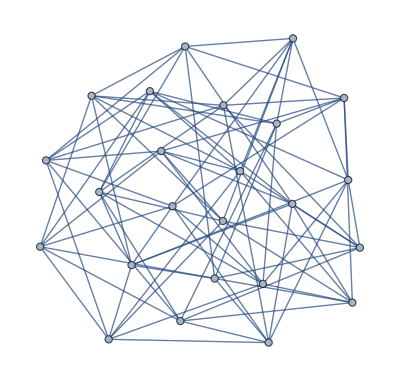

```mathematica
G=Import["/home/victorbankston/Documents/teaching/Spring25/Discrete_Math/labs/graph_28237.g6"]
```

Then we can calculate other parameters of the graph, like its connectivity.

```mathematica
VertexConnectivity[G]
```

7

## Quiz: (15 points)

Find a graph that has chromatic number at least 5, clique number equal to 2 and is Hamiltonian. Open the graph in Mathematica, calculate at least 1 parameter for this graph (like its connectivity) and take a screenshot. Be sure to include the House of Graphs identifying number in your screenshot.